```mathematica
SetDirectory[NotebookDirectory[]];
BurnRate=Import["BurnRate.csv","CSV"];
```

```mathematica
DD={};
For[i=0,i<Length[BurnRate],i++;DD=Append[DD,{BurnRate[[i]][[1]],BurnRate[[i]][[2]]}]]
D3He={};
For[i=0,i<Length[BurnRate],i++;D3He=Append[D3He,{BurnRate[[i]][[1]],BurnRate[[i]][[3]]}]]
HeHe={};
For[i=0,i<Length[BurnRate],i++;HeHe=Append[HeHe,{BurnRate[[i]][[1]],BurnRate[[i]][[4]]}]]
```

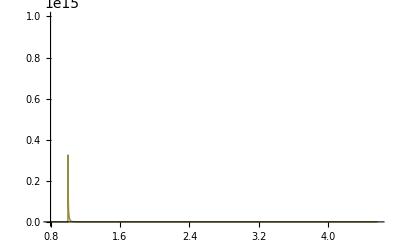

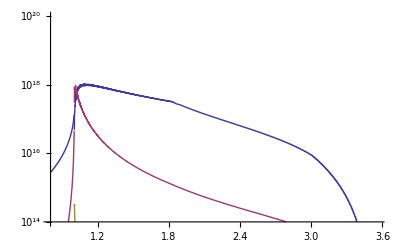

```mathematica
ListPlot[{DD,D3He,HeHe},Joined->True,PlotRange->{0,10^18}]
ListLogPlot[{DD,D3He,HeHe},Joined->True,PlotRange->{10^14,10^20}]
```